## NF theory for one unstable mode case

```mathematica
eval=Thread[{kaa,kba,kbc,kcb,kab,kac,kcc,μ,β,v,da,db,n}->{3.1623,3.1623,3.1623,3.1623,100,100,0.1,0.01,0.1,200,1,0.01,2}];
```

```mathematica
ha[m_,k_]:=m^n/(m^n+k^n)
hi[m_,k_]:=k^n/(m^n+k^n)
```

```mathematica
f[a_,b_,c_]:=v ha[a,kaa]hi[b,kba]-μ a+β
g[a_,b_,c_]:=v ha[a,kab]hi[c,kcb]-μ b+β
h[a_,b_,c_]:=v hi[a,kac]hi[b,kbc]ha[c,kcc]-μ c+β
```

```mathematica
fp=Flatten[NSolve[{f[a0,b0,c0],g[a0,b0,c0],h[a0,b0,c0]}/.eval,{a0,b0,c0},Reals]]
```

{b0→45.0828,c0→55.2733,a0→107.838}

```mathematica
zeros=Thread[{a,b,c}->ConstantArray[0,3]];
```

#### Jacobian matrix and dispersion relation

```mathematica
j=D[{f[a+a0,b+b0,c+c0],g[a+a0,b+b0,c+c0],h[a+a0,b+b0,c+c0]},{{a,b,c}}]/.eval/.fp/.zeros;
jd=j-k^2DiagonalMatrix[{da,db,0}];
```

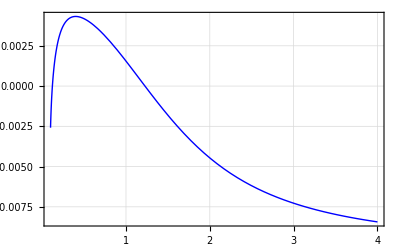

```mathematica
dispersion=Plot[Max[Re[Eigenvalues[jd/.eval]]],{k,0.1,4},PlotRange->All,Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14},PlotStyle->{Thick,Blue}]
```

#### Numerical solution

```mathematica
T=1000;
δ=10;
```

```mathematica
eqn={1/δ D[a[t,x],{t,1}]==da D[a[t,x],{x,2}]+f[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0],1/δ D[b[t,x],{t,1}]==db D[b[t,x],{x,2}]+g[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0],1/δ D[c[t,x],{t,1}]==h[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0]}/.eval/.fp;
ic={a[0,x]==0.01Cos[x],b[0,x]==0.01Cos[x],c[0,x]==0.01Cos[x]};
bc={a[t,-Pi]==a[t,Pi],b[t,-Pi]==b[t,Pi],c[t,-Pi]==c[t,Pi]};
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,-Pi,Pi}];
```

```mathematica
ListAnimate[Table[Plot[{asol[t,x],bsol[t,x],csol[t,x]},{x,-Pi,Pi},PlotRange->{-60,60}],{t,0,T,20}]]
```

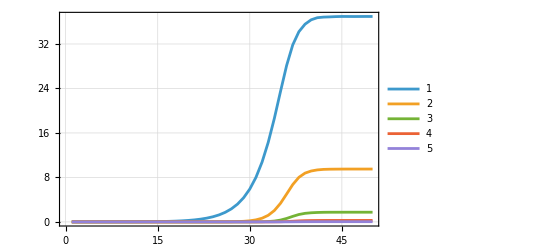

```mathematica
ListLinePlot[Table[Table[1/Pi NIntegrate[Cos[k x]csol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,1,T,20}],{k,1,5}],PlotRange->All,Frame->True,GridLines->Automatic,PlotLegends->Automatic]
```

```mathematica
data=Table[Table[1/Pi NIntegrate[Cos[k x]csol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,1,T,5}],{k,1,5}];
```

#### Fitting to NF equation

```mathematica
z=data[[1]];
times=Table[i,{i,Dimensions[z][[1]]}];
ztofit=Table[{times[[i]],z[[i]]},{i,Dimensions[z][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[ztofit,functofit,{{r0,0.1},{p1,01},{p2,0.01}},x]
```

FittedModel[…]

```mathematica
param=fit["BestFitParameters"]
```

{r0→0.000337087,p1→0.0833678,p2→0.0000606541}

```mathematica
timePoints={120,140,200};
pointCoords=Table[{timePoints[[i]],functofit/.x->timePoints[[i]]/.param},{i,3}]
```

{{120,7.30924},{140,27.0325},{200,37.0732}}

```mathematica
p=Plot[functofit/.param,{x,0,200},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"CMU Serif",14}];
simIn=ListLinePlot[Re[z],PlotStyle->{Thick,Dashed,Blue},BaseStyle->{FontFamily->"CMU Serif",14}];
```

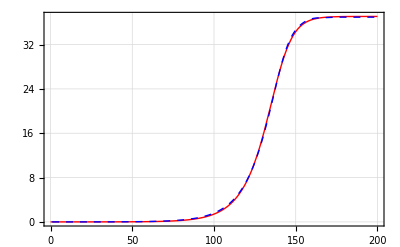

```mathematica
r1dyn=Show[{p,simIn},PlotRange->All,Frame->True,GridLines->Automatic]
```

#### Fitting pattern

```mathematica
z1t=functofit/.x->t/.param
```

(0.000337087 ⅇ^(0.0833678 t))/(√(1+8.26697×10^-11 ⅇ^(0.166736 t)))

```mathematica
{t1,t2,t3}={120,140,200}
```

{120,140,200}

```mathematica
z1t/.{{t->t1},{t->t2},{t->t3}}
```

{7.30924,27.0325,37.0732}

```mathematica
{c1,c2,c3}=1/(2Pi) NIntegrate[csol[5{t1,t2,t3},x],{x,-Pi,Pi}]
```

{-0.138573,-2.24272,-3.80295}

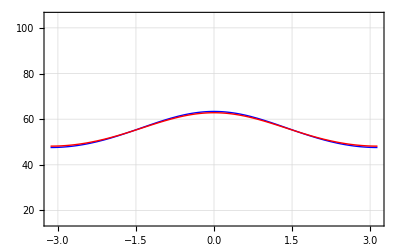

```mathematica
uplt1=Plot[{c0+csol[5t1,x]/.fp,(c1+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t1/.fp},{x,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

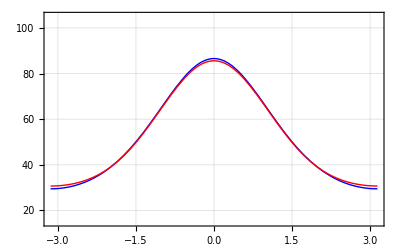

```mathematica
uplt2=Plot[{c0+csol[5t2,x]/.fp,(c2+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t2/.fp},{x,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

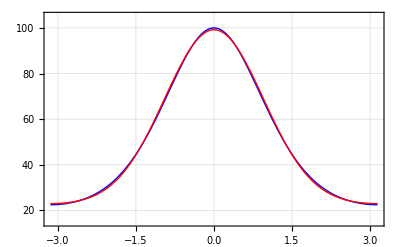

```mathematica
uplt3=Plot[{c0+csol[5t3,x]/.fp,(c3+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t3/.fp},{x,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

#### Rotation

```mathematica
ω=-Pi/6;
```

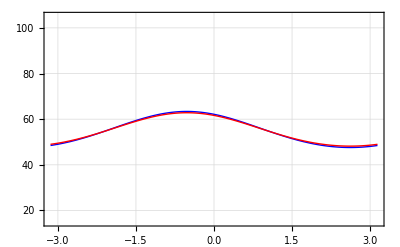

```mathematica
uplt1rot=Plot[{c0+csol[5t1,x]/.fp/.x->Mod[y-ω,2Pi,-Pi],(c1+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t1/.fp/.x->Mod[y-ω,2Pi,-Pi]},{y,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

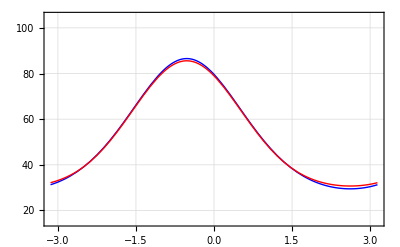

```mathematica
uplt2rot=Plot[{c0+csol[5t2,x]/.fp/.x->Mod[y-ω,2Pi,-Pi],(c2+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t2/.fp/.x->Mod[y-ω,2Pi,-Pi]},{y,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

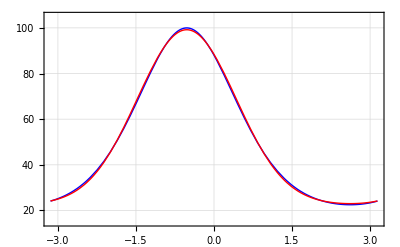

```mathematica
uplt3rot=Plot[{c0+csol[5t3,x]/.fp/.x->Mod[y-ω,2Pi,-Pi],(c3+(z1t Cos[x]+0.007z1t^2Cos[2x]+0.00002z1t^3Cos[3x]))+c0/.t->t3/.fp/.x->Mod[y-ω,2Pi,-Pi]},{y,-Pi,Pi},PlotRange->{15,105},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}]
```

#### z1 Streamplot

```mathematica
points=17;
θ2=Table[0+i/points Pi/2,{i,0,points,1}]//N;
```

```mathematica
r=5;
initialcondition=Table[{x[0]==r Cos[θ2[[i]]],y[0]==r Sin[θ2[[i]]]},{i,Dimensions[θ2][[1]]}];
```

```mathematica
solpp=Table[NDSolve[Flatten[{x'[t]==p1 x[t]-p2 x[t](x[t]^2+y[t]^2),y'[t]==p1 y[t]-p2 y[t](x[t]^2+y[t]^2),initialcondition[[i]]}]/.param,{x,y},{t,0,2000}],{i,Dimensions[initialcondition][[1]]}];
```

```mathematica
solpp2=NDSolve[{x'[t]==p1 x[t]-p2 x[t](x[t]^2+y[t]^2),y'[t]==p1 y[t]-p2 y[t](x[t]^2+y[t]^2),x[0]==0.01Sqrt[3],y[0]==0.01}/.param,{x,y},{t,0,2000}];
```

```mathematica
pp1mode=ParametricPlot[Table[{x[10t],y[10t]}/.solpp[[i]],{i,Dimensions[initialcondition][[1]]}],{t,0,200},PlotRange->All,Frame->True,PlotStyle->{Thickness[0.002],Gray},GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14},AspectRatio->True]/. Line[x_]:>{Arrowheads[ConstantArray[0.02,2]],Arrow[x]};
```

```mathematica
pp1mode2=ParametricPlot[{x[10t],y[10t]}/.solpp2,{t,0,200},PlotRange->All,Frame->True,PlotStyle->{RGBColor[0,0.6,0]},GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14},AspectRatio->True]/. Line[x_]:>{Arrowheads[ConstantArray[0.025,10]],Arrow[x]};
```

```mathematica
circ=Graphics[{RGBColor[0,0.,0],Circle[{0,0},Sqrt[p1/p2]/.param,{0,Pi/2}]}];
```

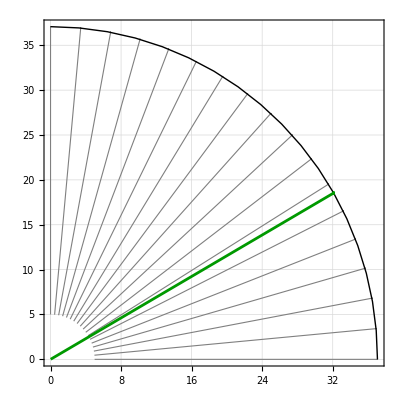

```mathematica
z1geometry=Show[pp1mode,circ,pp1mode2]
```